```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
b[t_]=Sqrt[1+t^2];
τ[t_]=ArcTan[t];
Subscript[Φ, n_][x_,t_]=b[t]^(-1/2)Subscript[ϕ, n][x/b[t]]*E^(I*(x^2*b'[t]/(2*b[t])-(n+1/2)τ[t]));
t ≥0;
Subscript[ψ, F][x_,y_,t_] = 1/Sqrt[2] * (Subscript[Φ, 0][x,t]Subscript[Φ, 1][y,t] - Subscript[Φ, 0][y,t]Subscript[Φ, 1][x,t] );
Subscript[ψ, B][x_,y_,t_]=Sign[y-x]Subscript[ψ, F][x,y,t];
Subscript[ρ, F][x_,y_]=Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],-Infinity,Infinity}];
ρ[x_,y_]=Subscript[ρ, F][x,y]-2*Sign[y-x]Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],x,y}];
Subscript[ρ, B][x_,y_,t_]=1/b[t]*ρ[x/b[t],y/b[t]]*E^(-I*(b'[t](x^2-y^2))/(2*b[t]));
Subscript[n, B][p_,t_] := 2/(2π)*NIntegrate[E^(I*p*(x-y))Subscript[ρ, B][x,y,t],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->6,PrecisionGoal->6];
```

```mathematica
Pdomain=Range[19,22,1];
Tdomain = {0,0.25,.5,0.75,1,1.5,2,4,8,12};
Subscript[dataSet, 10]= Re[Subscript[n, B][Pdomain,12 ]]
```

{0.0000112024,-0.000200723,-0.0014731,0.000145737}

```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
Subscript[ω, 0]=10;
Subscript[ω, 1]=1;
b[t_]=Sqrt[1+(Subscript[ω, 0]^2-Subscript[ω, 1]^2)/Subscript[ω, 1]^2 Sin[Subscript[ω, 1]*t]^2];
τ[t_]=ArcTan[(Subscript[ω, 0] Tan[t Subscript[ω, 1]])/Subscript[ω, 1]]/Subscript[ω, 0];
Subscript[Φ, n_][x_,t_]=b[t]^(-1/2)Subscript[ϕ, n][x/b[t]]*E^(I*(x^2*b'[t]/(2*b[t])-(n+1/2)τ[t]));
t ≥0;
Subscript[ψ, F][x_,y_,t_] = 1/Sqrt[2] * (Subscript[Φ, 0][x,t]Subscript[Φ, 1][y,t] - Subscript[Φ, 0][y,t]Subscript[Φ, 1][x,t] );
Subscript[ρ, F][x_,y_]=Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],-Infinity,Infinity}];
Subscript[ψ, A][x_,y_,t_,κ_]=E^(I*π*(1-κ)HeavisideTheta[y-x])Subscript[ψ, F][x,y,t];
Subscript[ρ, α][x_,y_,κ_]=Subscript[ρ, F][x,y]-Sign[y-x]*(E^(-Sign[y-x]*I*π*κ)+1)*Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0], {Subscript[x, 2],x, y}];
Subscript[ρ, A][x_,y_,t_,κ_]=1/b[t]*Subscript[ρ, α][x/b[t],y/b[t],κ]*E^((I*b'[t])/(2b[t])(y^2-x^2));
Subscript[n, A][p_,t_,κ_]:=Subscript[n, A][p,t,κ]=If[p≥0,
2/(2π)NIntegrate[E^(I*p*(x-y))Subscript[ρ, A][x,y,t,κ],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"GaussKronrodRule"}, AccuracyGoal->5,PrecisionGoal->5],
Subscript[n, A][-p,t,κ]];
```

```mathematica
Subscript[n, A][2,0.5,0]//AbsoluteTiming
```

{333.444,0.0693226-0.0000200681 ⅈ}

```mathematica
Subscript[n, A][1,0.5,0]//AbsoluteTiming
```

{364.149,0.0668523-0.0000591963 ⅈ}

```mathematica
r[t_]=Sqrt[1+t^2];
u[t_]=r'[t];
τ[t_]=Integrate[Sqrt[1-u[t]^2],t];
Solve[τ==τ[t],t]
```

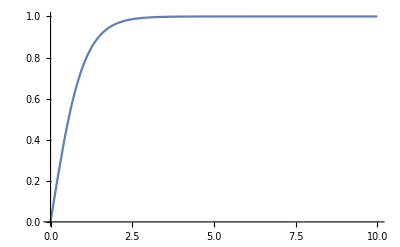

```mathematica
Plot[Tanh[t],{t,0,10},PlotRange->All]
```